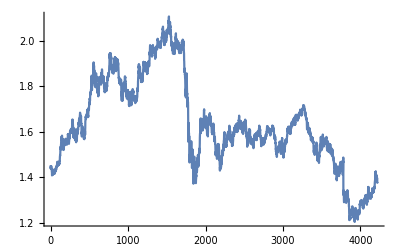

```mathematica
data=Import["/Users/wanghaibiao/Desktop/GBP USD 2002-2018.xlsx",{"Data",1,Table[i,{i,2,4220}],2}];
(*data import from 2002-01-02 to 2018-03-05*)
ListLinePlot[data]
(*plot the data, check the trend and whether it is a time series*)
```

```mathematica
(*we set the time line frim 0 to 4218, which is represent the trade date from 2002-01-02  to 2018-03-05. The data is changing by following time. And have trends in different time periods. However, the range of data change is a little bit large from around 1.2 to 2.2. We normally assume the financial data is exponential (we can find this from the trend of data), thus we decide to analyse the logarithmic data, not only make the range of data around 0 to 1, but also keep the same trends as the original data*)
```

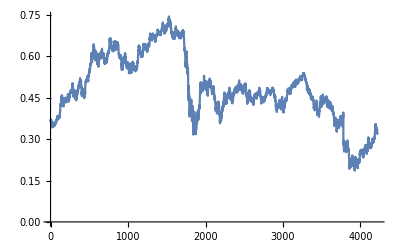

```mathematica
logdata=Log[data];(*take the ln data, two plots look similiar*)
ListLinePlot[Log[data]]
```

```mathematica
(*clearly, we can see the trends of data is random, there is no stable mean and volatility in different period of time, thus, the data is non-stationary*)
```

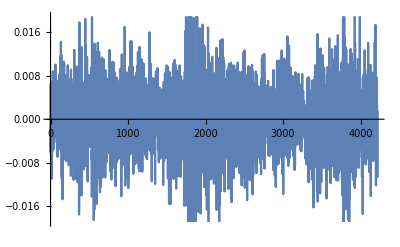

```mathematica
return=Differences[logdata];(*log return of the data, which is the first difference of the data*)
ListLinePlot[return]
```

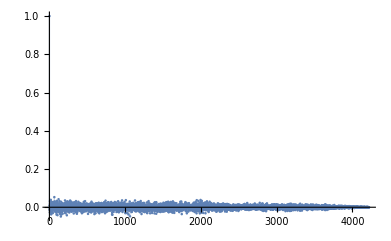

```mathematica
Print[ListPlot[CorrelationFunction[return,{4217}],Filling->Axis,PlotRange->All]]
```

```mathematica
AutocorrelationTest[return]
```

0.206794

```mathematica
(*The result shows the series of return is white noise, since the p-value is greater than 0.05, Subscript[H, 0]: Subscript[rho, 1]=Subscript[rho, 2]=...=Subscript[rho, m]=0  vs  Subscript[H, 1]: at least one Subscript[rho, k]<>0, k=1,2,3,4...,m. Thus, rho significantly is equal to zero.  *)
```

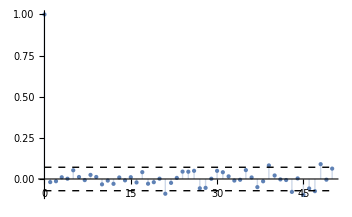

```mathematica
t={0,756};
Subscript[return, 1]=TimeSeries[Take[Drop[return,252],756],t];
acf[Subscript[return, 1]_,lmax_,clev_:0.95]:=Show[ListPlot[CorrelationFunction[data,{0,lmax}],Filling->Axis,PlotLabel->"ACF",PlotRange->{{0,lmax},All},PlotStyle->PointSize[Medium]],
Graphics[{Dashed,Line[{{0,#},{lmax,#}}]}]&/@(Quantile[NormalDistribution[],{(1-clev)/2,1-(1-clev)/2}]/(√(data["PathLengths"]⟦1⟧)))]
acf[Subscript[return, 1],50,.95]
```

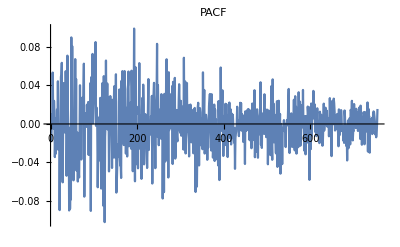

```mathematica
ListLinePlot[PartialCorrelationFunction[Subscript[return, 1],{755}],PlotLabel->"PACF"]
```

```mathematica
(*we set the lag is within 50, to find the p and q of ARMA(p,q) model by by plotting the partial autocorrelation functions for an estimate of p,and likewise using the autocorrelation functions for an estimate of q. However, ACF cut off at lag zero,  PACF tail off in a very large lag. Since we can't estimate a large lag ARMA model, because of the numbers of parameters, thus we use AIC to help us to choose the lag of the data*)
```

```mathematica
model1= TimeSeriesModelFit[Subscript[return, 1],"ARMA"];
model1["CandidateSelectionTable"]
```

| Candidate | AIC
1 | MAProcess[0] | -7834.84
2 | MAProcess[1] | -7833.12
3 | ARProcess[1] | -7833.11
4 | ARMAProcess[1,1] | -7831.15

```mathematica
(*MA(0) will be the choice of the model selection, and after check the residual of the model is whether white noise or not, then start to predict the model*)
```

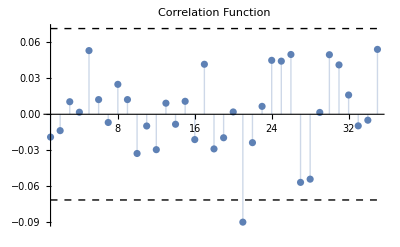

```mathematica
mdoel1= TimeSeriesModelFit[Subscript[return, 1],{"MA",{0}}];
model1["ACFPlot"]
```

```mathematica
(*ACF is around zero,from lag zero.*)
```

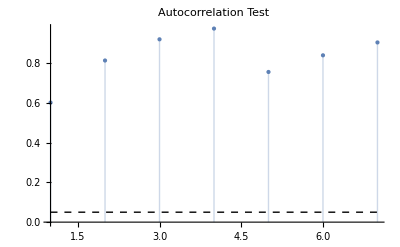

```mathematica
model1["LjungBoxPlot"]
```

```mathematica
(*According to the Ljung Box Test, all the values are greater than 0.05, which means Subscript[H, 0]: rho1=rho2=rho3=...rho-m=0 is accepted, Then the residuals of MA(0) are white noise. Also, there is no parameters in MA(0) model, we don't need to check the whether the parameter estimation is significant or not. Thus, we can predict the MA(0)*)
```

```mathematica
(*We know that after one difference we obtain the stationary series, thus, we can also build ARIMA model on the non-stationary data. Base on the ACF and PACF, we assume ARIMA(1,1,0), ARIMA(0,1,1), ARIMA(1,1,1) OR ARIMA(0,1,0)*)
Subscript[logdata, 1]=TimeSeries[Take[Drop[logdata,252],756],t];
model2=TimeSeriesModelFit[Subscript[logdata, 1]];
model2["CandidateSelectionTable"]
```

| Candidate | AIC
1 | ARIMAProcess[0,1,0] | -7833.85
2 | ARIMAProcess[0,1,1] | -7832.13
3 | ARIMAProcess[1,1,0] | -7832.12
4 | ARIMAProcess[1,1,1] | -7830.16
5 | ARIMAProcess[2,2,1] | -7810.89
6 | ARIMAProcess[2,2,2] | -7807.34
7 | ARIMAProcess[3,2,1] | -7805.49
8 | ARIMAProcess[3,2,2] | -7800.28
9 | ARIMAProcess[1,2,2] | -7799.43
10 | ARIMAProcess[1,2,1] | -7799.05

```mathematica
(*we can see ARIMA(0,1,0), which is the random walk, is the best fit  on the non-stationary series*)
```

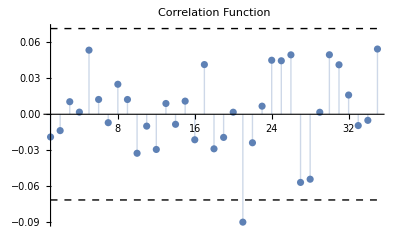

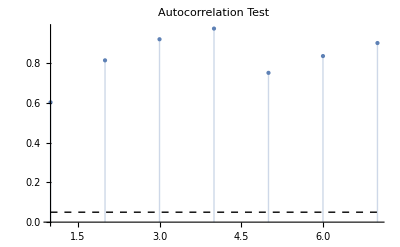

```mathematica
mdoel2= TimeSeriesModelFit[Subscript[return, 1],{"ARIMA",{0,1,0}}];
model2["ACFPlot"]
model2["LjungBoxPlot"]
```

```mathematica
(*All the residuals are white nosie, then we can predict the non-stationary time series via ARIMA(0,1,0)*)
```

```mathematica
(*Let's also look at the residual volatility, and see if it have ARCH effect*)
```

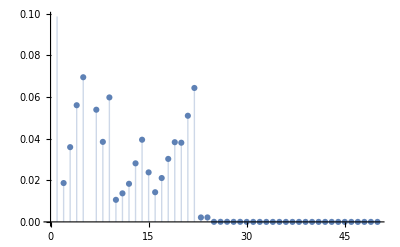

```mathematica
residual=model1["FitResiduals"];
sresidual=residual^2;
ListPlot[Table[AutocorrelationTest[sresidual,i,"LjungBox"],{i,1,50}],Filling->Axis]
```

```mathematica
(*the p-value shows that it is not significantly smaller than 0.05, we accept the Subscript[H, 0], which there is no ARCH effect*)
```